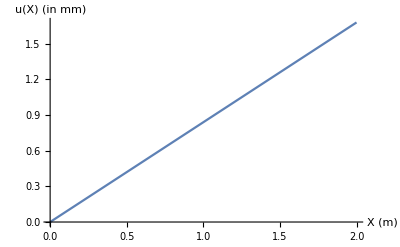

```mathematica
L=2; (*in m*)
α=12 10^-6; (*1/degree centigrade*)
Ε=1.0 10^11; (*in Pa*)
ΔT=80-10; (*in degree centigrade*)(**)
δ=α ΔT L//N;(*"//N" gives you numerical values*)
u[X_]:=α ΔT X
Plot[u[X] 10^3,{X,0,L},AxesLabel->{"X (m)","u(X) (in mm)"}]
```

```mathematica
δ=α ΔT L//N
```

0.00168

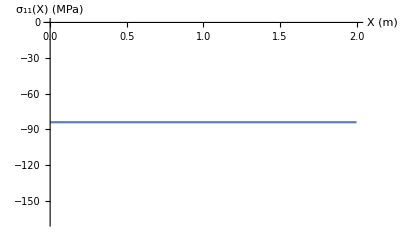

```mathematica
Plot[-Ε α ΔT/1000000,{X,0,L},AxesLabel->{"X (m)","σ_11(X) (MPa)"}]
```

1/1000

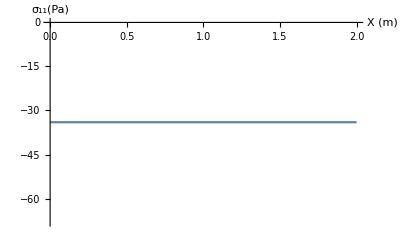

```mathematica
Subscript[u, 0]= 10^-3
Plot[(Ε(Subscript[u, 0]-α ΔT L))/(L 1000000),{X,0,L},AxesLabel->{"X (m)","σ_11(Pa)"}]
```

1/1000

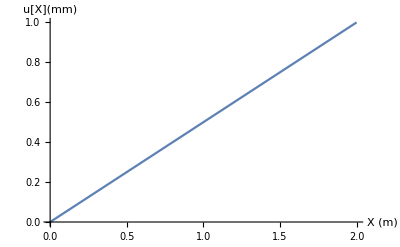

```mathematica
Subscript[u, 0]= 10^-3
Plot[(Subscript[u, 0] X)/L 1000,{X,0,L},AxesLabel->{"X (m)","u[X](mm)"}]
```

```mathematica
With[{},
(*{L=1,D0=0.2,P=1},*)
(*Plot[P/(L-2 y+2 D0)^2,{y,0,L/2},PlotRange->All];*)
Integrate[P/(π((L-2 y+2 D0)^2-4 Di^2)),{y,0,L/2}]
]
```

$Aborted

```mathematica
Expand[π((L-2 y+2 D0)^2-4 Di^2)]//Simplify
```

4 π (D0^2-Di^2-2 D0 (-1+y)+(-1+y)^2)

#### Additional note:

To type Greek letters such as Δ, α, refer to “https://reference.wolfram.com/language/guide/GreekLetters.html”
To type subscripts/superscripts, refer to “https://reference.wolfram.com/language/workflow/EnterSubscriptsAndSuperscripts.html”